# Mu3e sensitivity to parameter space

Find our list of signal and background events, along with associated parameters

```mathematica
sigdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events","*"}];
bkgdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events","*"}];
sigfiles=FileNames[FileNameJoin[{sigdirs,"unweighted_events.lhe.gz"}]];
bkgfiles=FileNames[FileNameJoin[{bkgdirs,"unweighted_events.lhe.gz"}]];
paramfiles=FileNames[FileNameJoin[{sigdirs,"report.dat"}]];
files=Transpose[{sigfiles,bkgfiles,paramfiles}];
nRuns=files//Length;
nb=FileNameJoin[{NotebookDirectory[],"analyze-run.nb"}];
```

Call our analysis notebook on each set and let us know if it is sensitive or not

```mathematica
paramspace={};
Do[
sig=files[[i,1]];
bkg=files[[i,2]];
params=Import[files[[i,3]]];
mphi=params[[3,2]];
gsm=params[[4,2]];
gse=params[[5,2]];
pattern="m_ϕ=``, g_ϕμ=``, g_ϕe=``:";
sensitive=NotebookEvaluate[nb];
paramspace=Append[paramspace,{mphi,gsm,gse,sensitive}];
If[sensitive,Print[StringForm[pattern<>" sensitive",mphi,gsm,gse]];
,Print[StringForm[pattern<>" NOT sensitive",mphi,gsm,gse]]],
{i,nRuns}]
```

m_ϕ=0.0015, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0688947, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.074079, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0792632, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0844474, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0896316, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0896316, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0948158, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0948158, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.1, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.1, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

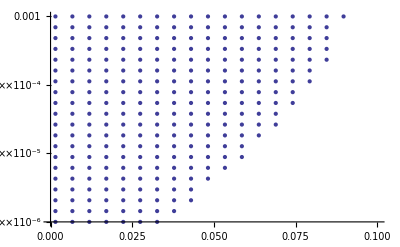

```mathematica
validparams=If[#1[[4]],{#1[[1]],#1[[2]]},##&[]]&/@paramspace;
ListLogPlot[validparams,PlotRange->{{0,0.1},{1*^-6,1*^-3}}]
```

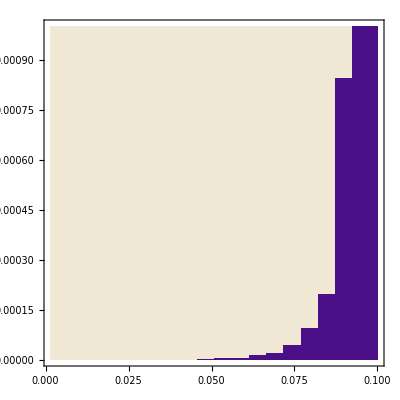

```mathematica
pl=Normal@ListContourPlot[If[#[[4]],{#[[1]],#[[2]],1},{#[[1]],#[[2]],0}]&/@paramspace,Contours->1,InterpolationOrder->0]
(*ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]*)
```